# Test and Filter Runs

n: number of stars
NS: number of simulations
R: virial radius
Isolated System

### Logs

```mathematica
Print[$RunNumber]
```

200

```mathematica
Print[script`path]
```

/home/cesarg/git/workspace/nbody6/isolated/scripts/FilterAndTest

```mathematica
logstream = OpenWrite[
FileNameJoin[{script`path, "nbstatus" <> ToString[$RunNumber] <> ".log"}],
FormatType->OutputForm
]
```

OutputStream[…]

```mathematica
Write[logstream, "Begin log ...."];
```

## Initialization

```mathematica
{$MachineName,$Version}
```

{tars,12.1.0 for Linux x86 (64-bit) (March 18, 2020)}

```mathematica
AppendTo[$Path,Environment["MYGITDIR"]];
```

```mathematica
Get["AstroTools`nbody6`"]
```

```mathematica
Get["AstroTools`Utilities`"]
```

```mathematica
$ConfiguredKernels = 
 List[SubKernels`LocalKernels`LocalMachine[30, 
   Rule[SubKernels`LocalKernels`LowerPriority, True]]]
```

{«30 local kernels»}

```mathematica
resultsPath=FileNameJoin[{Environment["MYGITDIR"],"workspace","nbody6","isolated","n"<>ToString[$RunNumber],"NSX-R1","results"}]
```

/home/cesarg/git/workspace/nbody6/isolated/n200/NSX-R1/results

```mathematica
SetDirectory[resultsPath]
```

/home/cesarg/git/workspace/nbody6/isolated/n200/NSX-R1/results

```mathematica
FileNames[]
```

{goodRuns.log,run-1,run-10,run-100,run-1000,run-101,run-102,run-103,run-104,run-105,run-106,run-107,run-108,run-109,run-11,run-110,run-111,run-112,run-113,run-114,run-115,run-116,run-117,run-118,run-119,run-12,run-120,run-121,run-122,run-123,run-124,run-125,run-126,run-127,run-128,run-129,run-13,run-130,run-131,run-132,run-133,run-134,run-135,run-136,run-137,run-138,run-139,run-14,run-140,run-141,run-142,run-143,run-144,run-145,run-146,run-147,run-148,run-149,run-15,run-150,run-151,run-152,run-153,run-154,run-155,run-156,run-157,run-158,run-159,run-16,run-160,run-161,run-162,run-163,run-164,run-165,run-166,run-167,run-168,run-169,run-17,run-170,run-171,run-172,run-173,run-174,run-175,run-176,run-177,run-178,run-179,run-18,run-180,run-181,run-182,run-183,run-184,run-185,run-186,run-187,run-188,run-189,run-19,run-190,run-191,run-192,run-193,run-194,run-195,run-196,run-197,run-198,run-199,run-2,run-20,run-200,run-201,run-202,run-203,run-204,run-205,run-206,run-207,run-208,run-209,run-21,run-210,run-211,run-212,run-213,run-214,run-215,run-216,run-217,run-218,run-219,run-22,run-220,run-221,run-222,run-223,run-224,run-225,run-226,run-227,run-228,run-229,run-23,run-230,run-231,run-232,run-233,run-234,run-235,run-236,run-237,run-238,run-239,run-24,run-240,run-241,run-242,run-243,run-244,run-245,run-246,run-247,run-248,run-249,run-25,run-250,run-251,run-252,run-253,run-254,run-255,run-256,run-257,run-258,run-259,run-26,run-260,run-261,run-262,run-263,run-264,run-265,run-266,run-267,run-268,run-269,run-27,run-270,run-271,run-272,run-273,run-274,run-275,run-276,run-277,run-278,run-279,run-28,run-280,run-281,run-282,run-283,run-284,run-285,run-286,run-287,run-288,run-289,run-29,run-290,run-291,run-292,run-293,run-294,run-295,run-296,run-297,run-298,run-299,run-3,run-30,run-300,run-301,run-302,run-303,run-304,run-305,run-306,run-307,run-308,run-309,run-31,run-310,run-311,run-312,run-313,run-314,run-315,run-316,run-317,run-318,run-319,run-32,run-320,run-321,run-322,run-323,run-324,run-325,run-326,run-327,run-328,run-329,run-33,run-330,run-331,run-332,run-333,run-334,run-335,run-336,run-337,run-338,run-339,run-34,run-340,run-341,run-342,run-343,run-344,run-345,run-346,run-347,run-348,run-349,run-35,run-350,run-351,run-352,run-353,run-354,run-355,run-356,run-357,run-358,run-359,run-36,run-360,run-361,run-362,run-363,run-364,run-365,run-366,run-367,run-368,run-369,run-37,run-370,run-371,run-372,run-373,run-374,run-375,run-376,run-377,run-378,run-379,run-38,run-380,run-381,run-382,run-383,run-384,run-385,run-386,run-387,run-388,run-389,run-39,run-390,run-391,run-392,run-393,run-394,run-395,run-396,run-397,run-398,run-399,run-4,run-40,run-400,run-401,run-402,run-403,run-404,run-405,run-406,run-407,run-408,run-409,run-41,run-410,run-411,run-412,run-413,run-414,run-415,run-416,run-417,run-418,run-419,run-42,run-420,run-421,run-422,run-423,run-424,run-425,run-426,run-427,run-428,run-429,run-43,run-430,run-431,run-432,run-433,run-434,run-435,run-436,run-437,run-438,run-439,run-44,run-440,run-441,run-442,run-443,run-444,run-445,run-446,run-447,run-448,run-449,run-45,run-450,run-451,run-452,run-453,run-454,run-455,run-456,run-457,run-458,run-459,run-46,run-460,run-461,run-462,run-463,run-464,run-465,run-466,run-467,run-468,run-469,run-47,run-470,run-471,run-472,run-473,run-474,run-475,run-476,run-477,run-478,run-479,run-48,run-480,run-481,run-482,run-483,run-484,run-485,run-486,run-487,run-488,run-489,run-49,run-490,run-491,run-492,run-493,run-494,run-495,run-496,run-497,run-498,run-499,run-5,run-50,run-500,run-501,run-502,run-503,run-504,run-505,run-506,run-507,run-508,run-509,run-51,run-510,run-511,run-512,run-513,run-514,run-515,run-516,run-517,run-518,run-519,run-52,run-520,run-521,run-522,run-523,run-524,run-525,run-526,run-527,run-528,run-529,run-53,run-530,run-531,run-532,run-533,run-534,run-535,run-536,run-537,run-538,run-539,run-54,run-540,run-541,run-542,run-543,run-544,run-545,run-546,run-547,run-548,run-549,run-55,run-550,run-551,run-552,run-553,run-554,run-555,run-556,run-557,run-558,run-559,run-56,run-560,run-561,run-562,run-563,run-564,run-565,run-566,run-567,run-568,run-569,run-57,run-570,run-571,run-572,run-573,run-574,run-575,run-576,run-577,run-578,run-579,run-58,run-580,run-581,run-582,run-583,run-584,run-585,run-586,run-587,run-588,run-589,run-59,run-590,run-591,run-592,run-593,run-594,run-595,run-596,run-597,run-598,run-599,run-6,run-60,run-600,run-601,run-602,run-603,run-604,run-605,run-606,run-607,run-608,run-609,run-61,run-610,run-611,run-612,run-613,run-614,run-615,run-616,run-617,run-618,run-619,run-62,run-620,run-621,run-622,run-623,run-624,run-625,run-626,run-627,run-628,run-629,run-63,run-630,run-631,run-632,run-633,run-634,run-635,run-636,run-637,run-638,run-639,run-64,run-640,run-641,run-642,run-643,run-644,run-645,run-646,run-647,run-648,run-649,run-65,run-650,run-651,run-652,run-653,run-654,run-655,run-656,run-657,run-658,run-659,run-66,run-660,run-661,run-662,run-663,run-664,run-665,run-666,run-667,run-668,run-669,run-67,run-670,run-671,run-672,run-673,run-674,run-675,run-676,run-677,run-678,run-679,run-68,run-680,run-681,run-682,run-683,run-684,run-685,run-686,run-687,run-688,run-689,run-69,run-690,run-691,run-692,run-693,run-694,run-695,run-696,run-697,run-698,run-699,run-7,run-70,run-700,run-701,run-702,run-703,run-704,run-705,run-706,run-707,run-708,run-709,run-71,run-710,run-711,run-712,run-713,run-714,run-715,run-716,run-717,run-718,run-719,run-72,run-720,run-721,run-722,run-723,run-724,run-725,run-726,run-727,run-728,run-729,run-73,run-730,run-731,run-732,run-733,run-734,run-735,run-736,run-737,run-738,run-739,run-74,run-740,run-741,run-742,run-743,run-744,run-745,run-746,run-747,run-748,run-749,run-75,run-750,run-751,run-752,run-753,run-754,run-755,run-756,run-757,run-758,run-759,run-76,run-760,run-761,run-762,run-763,run-764,run-765,run-766,run-767,run-768,run-769,run-77,run-770,run-771,run-772,run-773,run-774,run-775,run-776,run-777,run-778,run-779,run-78,run-780,run-781,run-782,run-783,run-784,run-785,run-786,run-787,run-788,run-789,run-79,run-790,run-791,run-792,run-793,run-794,run-795,run-796,run-797,run-798,run-799,run-8,run-80,run-800,run-801,run-802,run-803,run-804,run-805,run-806,run-807,run-808,run-809,run-81,run-810,run-811,run-812,run-813,run-814,run-815,run-816,run-817,run-818,run-819,run-82,run-820,run-821,run-822,run-823,run-824,run-825,run-826,run-827,run-828,run-829,run-83,run-830,run-831,run-832,run-833,run-834,run-835,run-836,run-837,run-838,run-839,run-84,run-840,run-841,run-842,run-843,run-844,run-845,run-846,run-847,run-848,run-849,run-85,run-850,run-851,run-852,run-853,run-854,run-855,run-856,run-857,run-858,run-859,run-86,run-860,run-861,run-862,run-863,run-864,run-865,run-866,run-867,run-868,run-869,run-87,run-870,run-871,run-872,run-873,run-874,run-875,run-876,run-877,run-878,run-879,run-88,run-880,run-881,run-882,run-883,run-884,run-885,run-886,run-887,run-888,run-889,run-89,run-890,run-891,run-892,run-893,run-894,run-895,run-896,run-897,run-898,run-899,run-9,run-90,run-900,run-901,run-902,run-903,run-904,run-905,run-906,run-907,run-908,run-909,run-91,run-910,run-911,run-912,run-913,run-914,run-915,run-916,run-917,run-918,run-919,run-92,run-920,run-921,run-922,run-923,run-924,run-925,run-926,run-927,run-928,run-929,run-93,run-930,run-931,run-932,run-933,run-934,run-935,run-936,run-937,run-938,run-939,run-94,run-940,run-941,run-942,run-943,run-944,run-945,run-946,run-947,run-948,run-949,run-95,run-950,run-951,run-952,run-953,run-954,run-955,run-956,run-957,run-958,run-959,run-96,run-960,run-961,run-962,run-963,run-964,run-965,run-966,run-967,run-968,run-969,run-97,run-970,run-971,run-972,run-973,run-974,run-975,run-976,run-977,run-978,run-979,run-98,run-980,run-981,run-982,run-983,run-984,run-985,run-986,run-987,run-988,run-989,run-99,run-990,run-991,run-992,run-993,run-994,run-995,run-996,run-997,run-998,run-999}

### n–body parameters

```mathematica
(*
numberOfStars=380;
nb["S0"]=0.3(numberOfStars/1000)^(1/3)
nb["nMAX"]=2.(numberOfStars)^(1/2)
*)
```

```mathematica
FilePrint["../create-ini.sh"]
```

#!/bin/bash

echo "[`date`] Start"

mkdir results

cd results/
for filenumber in {1..1000..1}
do
	mkdir "./run-$filenumber/"
  	cat << EOF > ./run-$filenumber/ini.dat
1 20.0
200 1 10 $RANDOM 32 1
0.02 0.01 0.17 1.0 1.0 1001.0 1.0E-03 1 0.5
0 0 1 0 1 0 0 0 0 0
0 0 0 0 0 0 0 0 0 6
0 0 0 0 0 0 0 0 0 0
0 0 0 0 0 0 0 0 0 1
0 0 0 0 0 0 0 0 0 0
4.0E-05 0.001 0.2 1.0 1.0E-06 0.001
2.3 50.0 0.2 0 0 0.002 0 5.0
0.5 0 0 0 0.25
EOF
	echo $filenumber
done

cd ..
echo `pwd`
echo "[`date`] End"
echo "time elapsed: $SECONDS"
echo all done

```mathematica
strCreateFile=Import["../create-ini.sh","Table"]
```

{{#!/bin/bash},{},{echo,[`date`] Start},{},{mkdir,results},{},{cd,results/},{for,filenumber,in,{1..1000..1}},{do},{mkdir,./run-$filenumber/},{cat,<<,EOF,>,./run-$filenumber/ini.dat},{1,20.},{200,1,10,$RANDOM,32,1},{0.02,0.01,0.17,1.,1.,1001.,0.001,1,0.5},{0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,6},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0},{0.00004,0.001,0.2,1.,1.×10^-6,0.001},{2.3,50.,0.2,0,0,0.002,0,5.},{0.5,0,0,0,0.25},{EOF},{echo,$filenumber},{done},{},{cd,..},{echo,`pwd`},{echo,[`date`] End},{echo,time elapsed: $SECONDS},{echo,all,done}}

```mathematica
pos=Position[strCreateFile,"$RANDOM"][[1,1]];
numberOfStars=strCreateFile[[pos,1]]
nbodyStep=Floor@(strCreateFile[[pos+1,5]])
maxNbodyTime=Floor@(strCreateFile[[pos+1,6]]-nbodyStep)
```

200

1

1000

### Other global variables

#### Data

```mathematica
goodFiles=FileNameJoin[First[#]]&/@GatherBy[StringSplit[Import["goodRuns.log"][[All,2]],"/"],#[[-2]]&];
```

```mathematica
dirs=DirectoryName/@goodFiles;
```

```mathematica
runmax=Length[dirs]
```

204

```mathematica
If[!FileExistsQ["nbody6-data.mx"]
,
Print["Loading from source ..."];
data=ReadOutput/@goodFiles;
DumpSave["nbody6-data.mx",data];
,
Print["Loading from MX ..."];
Get["nbody6-data.mx"];
]//AbsoluteTiming
```

Loading from source ...

ReadList::readn: Invalid real number found when reading from «1».

General::stop: Further output of «1» will be suppressed during this calculation.

{65.3567,Null}

```mathematica
parameters=data[[All,1]];
```

```mathematica
parameters//Length
```

204

```mathematica
data=data[[All,2]];
```

```mathematica
lengthOfRuns=Tally[Length/@data]
```

{{1001,204}}

#### Parameters

```mathematica
(* NOTE 1: parameters V^*, T^*, M^* are different for each run *)
(* NOTE 2: $MeanMass numberOfStats ≈ $MassScale *)
parameters[[All,4]]
```

{1.156,1.207,1.198,0.991,1.235,1.041,1.135,1.174,1.098,1.212,1.253,1.174,1.039,1.066,0.887,1.258,1.274,1.184,1.332,0.941,1.132,1.187,1.063,1.24,1.299,1.202,1.224,1.21,0.958,1.25,1.218,1.259,1.23,1.209,1.307,1.049,1.185,1.205,1.155,1.253,1.205,1.261,1.138,1.126,1.165,1.151,1.175,1.268,1.118,1.119,1.162,1.265,1.134,1.211,1.209,1.083,1.202,1.031,1.258,1.18,1.18,1.181,1.242,1.292,1.221,0.945,1.141,1.237,1.192,1.214,1.17,1.13,0.975,1.137,1.217,1.248,1.169,1.213,1.186,1.252,1.171,1.034,1.212,1.164,1.162,1.055,1.077,1.14,1.17,1.142,1.144,1.206,1.206,1.194,1.186,1.199,1.161,1.18,1.282,1.176,1.106,1.272,1.137,1.154,1.21,1.314,1.208,1.229,1.204,1.225,1.185,1.248,1.117,1.047,1.276,1.22,1.171,1.236,0.933,1.215,1.215,1.063,1.166,1.119,1.295,1.279,1.173,1.159,1.065,1.101,1.114,1.28,1.084,1.178,1.448,1.155,1.139,1.243,1.222,1.14,1.084,1.183,1.296,1.305,1.05,1.158,1.118,1.255,1.203,1.248,1.164,1.07,1.166,1.183,1.111,1.226,1.233,1.198,1.148,1.081,1.209,1.467,1.222,1.241,1.2,1.189,1.2,1.166,1.264,1.181,1.153,1.15,0.919,1.16,1.201,1.162,1.292,1.291,1.035,1.448,1.028,1.201,1.136,1.199,1.044,1.268,1.102,1.197,1.097,1.204,1.331,1.12,1.185,1.276,1.053,1.243,1.177,1.246,0.959,1.077,1.099,1.262,1.037,1.196}

```mathematica
{$LengthScale,$MassScale,$SpeedScale,$TimeScale,$MeanMass,$SU}=Mean[parameters]
```

{1.,164.061,0.837289,1.17483,0.820392,4.4×10^7}

```mathematica
$EnergyScale=$MassScale ($SpeedScale)^2
```

115.015

```mathematica
$DensityScale=$MassScale/($LengthScale)^3
```

164.061

```mathematica
(* in units of Msun/pc^3*)
ρSunNeighborPhysical=0.09;
ρForClusterDisruptionPhysical=0.08;
```

```mathematica
(* in units of n-body units *)
ρSunNeighbor=ρSunNeighborPhysical/$DensityScale;
ρForClusterDisruption=ρForClusterDisruptionPhysical/$DensityScale;
```

```mathematica
(* checking units *)
ρSunNeighbor
```

0.000548577

```mathematica
(* mean density in nbody units *)
$MeanDensity=1./(4/3Pi(1)^3)
```

0.238732

```mathematica
(* mean density physical Msun/pc^3 *)
$MeanDensity $DensityScale
```

39.1666

```mathematica
(* Max elpased time for evolution in MY*)
maxNbodyTime*$TimeScale
```

1174.83

```mathematica
(* INITIAL TIME = 0 -> following nbody6 *)
timeArray=Range[0,maxNbodyTime,nbodyStep];
(* log step array: 0 time at -1 *)
log10TimeArray1=N@Prepend[Log10[Rest[timeArray]],0];
log10TimeArrayScaled1=N@Prepend[Log10[Rest[$TimeScale timeArray]],0];
```

```mathematica
Length/@{timeArray,log10TimeArray1,log10TimeArrayScaled1}
```

{1001,1001,1001}

## Delete invalid runs

```mathematica
dirsToDelete=Complement[Select[FileNames[],DirectoryQ],Part[StringSplit[#,$PathnameSeparator]&/@dirs,All,2]];
```

```mathematica
dirsToDelete=Flatten[StringCases[dirsToDelete,"run-"~~__]];
```

```mathematica
dirsToDelete//Short
```

{run-100,run-1000,run-101,run-103,run-105,run-106,run-107,run-108,run-109,run-11,run-111,run-112,run-113,run-114,run-115,run-116,run-118,run-119,run-120,run-121,run-122,run-123,run-124,run-125,run-127,run-128,run-129,run-13,run-130,run-132,run-133,run-134,run-135,run-136,run-139,run-14,run-140,run-141,run-142,run-143,run-145,run-146,run-147,run-148,run-149,run-15,run-150,run-151,run-152,run-153,run-154,run-155,run-156,run-157,run-158,run-159,run-16,run-160,run-161,run-162,run-163,run-164,run-166,run-167,run-168,run-169,run-17,run-172,run-173,run-174,run-175,run-177,run-178,run-179,run-18,run-180,run-181,run-182,run-183,run-184,run-186,run-187,run-188,run-189,run-190,run-191,run-192,run-193,run-194,run-196,run-197,run-198,run-199,run-20,run-200,run-201,run-202,run-204,run-205,run-206,run-207,run-208,run-209,run-21,run-210,run-211,run-212,run-213,run-214,run-215,run-216,run-217,run-218,run-219,run-22,run-220,run-221,run-222,run-223,run-224,run-225,run-227,run-230,run-231,run-232,run-233,run-235,run-236,run-238,run-239,run-24,run-240,run-241,run-242,run-243,run-244,run-247,run-248,run-25,run-250,run-252,run-253,run-254,run-255,run-256,run-257,run-259,run-26,run-261,run-262,run-263,run-264,run-265,run-266,run-268,run-269,run-270,run-271,run-273,run-274,run-275,run-276,run-277,run-279,run-28,run-281,run-282,run-283,run-285,run-287,run-288,run-29,run-290,run-291,run-292,run-293,run-294,run-296,run-298,run-299,run-3,run-30,run-300,run-301,run-302,run-303,run-304,run-305,run-307,run-308,run-31,run-310,run-311,run-312,run-313,run-314,run-315,run-316,run-317,run-318,run-319,run-32,run-320,run-321,run-322,run-323,run-325,run-326,run-327,run-33,run-330,run-331,run-332,run-334,run-336,run-337,run-338,run-339,run-34,run-340,run-341,run-342,run-343,run-344,run-345,run-346,run-347,run-348,run-349,run-350,run-352,run-353,run-354,run-355,run-356,run-357,run-358,run-359,run-36,run-360,run-361,run-362,run-363,run-366,run-368,run-369,run-37,run-370,run-372,run-374,run-375,run-376,run-377,run-378,run-38,run-380,run-381,run-382,run-383,run-384,run-385,run-386,run-387,run-388,run-39,run-390,run-392,run-393,run-394,run-395,run-396,run-398,run-399,run-4,run-40,run-400,run-401,run-402,run-404,run-405,run-406,run-408,run-409,run-41,run-410,run-412,run-413,run-414,run-415,run-418,run-419,run-42,run-420,run-421,run-422,run-423,run-424,run-425,run-426,run-429,run-43,run-430,run-431,run-432,run-433,run-434,run-436,run-437,run-438,run-439,run-440,run-441,run-443,run-444,run-445,run-446,run-447,run-448,run-449,run-45,run-450,run-451,run-452,run-453,run-454,run-456,run-457,run-459,run-46,run-460,run-462,run-465,run-466,run-467,run-468,run-47,run-470,run-471,run-472,run-473,run-475,run-476,run-48,run-482,run-483,run-484,run-488,run-49,run-490,run-492,run-493,run-495,run-497,run-498,run-499,run-5,run-50,run-501,run-502,run-504,run-506,run-507,run-508,run-509,run-51,run-512,run-513,run-514,run-515,run-516,run-517,run-518,run-519,run-520,run-521,run-525,run-526,run-527,run-528,run-529,run-53,run-532,run-535,run-537,run-538,run-539,run-54,run-540,run-541,run-544,run-545,run-546,run-548,run-549,run-55,run-550,run-551,run-552,run-554,run-557,run-558,run-559,run-56,run-560,run-561,run-562,run-564,run-565,run-566,run-567,run-568,run-569,run-57,run-570,run-571,run-572,run-573,run-574,run-575,run-576,run-577,run-578,run-579,run-58,run-580,run-582,run-583,run-584,run-585,run-586,run-587,run-588,run-589,run-59,run-590,run-591,run-592,run-593,run-595,run-596,run-597,run-598,run-599,run-60,run-600,run-601,run-602,run-605,run-606,run-607,run-608,run-609,run-610,run-612,run-613,run-614,run-615,run-616,run-617,run-618,run-619,run-62,run-620,run-621,run-622,run-624,run-626,run-627,run-629,run-63,run-630,run-631,run-632,run-633,run-634,run-636,run-637,run-638,run-64,run-640,run-641,run-642,run-643,run-644,run-645,run-646,run-647,run-648,run-649,run-65,run-650,run-651,run-652,run-654,run-655,run-656,run-658,run-659,run-66,run-660,run-661,run-662,run-663,run-664,run-666,run-667,run-668,run-669,run-67,run-670,run-671,run-672,run-673,run-674,run-675,run-676,run-677,run-679,run-68,run-680,run-681,run-682,run-683,run-684,run-687,run-688,run-689,run-69,run-690,run-691,run-692,run-693,run-694,run-695,run-696,run-697,run-698,run-7,run-70,run-700,run-701,run-703,run-704,run-705,run-708,run-709,run-71,run-710,run-712,run-713,run-714,run-715,run-716,run-720,run-721,run-723,run-725,run-726,run-728,run-729,run-73,run-730,run-731,run-732,run-733,run-734,run-735,run-737,run-738,run-739,run-74,run-740,run-741,run-742,run-743,run-745,run-746,run-749,run-75,run-752,run-753,run-754,run-756,run-757,run-758,run-759,run-76,run-760,run-761,run-762,run-763,run-764,run-766,run-767,run-768,run-769,run-77,run-772,run-773,run-774,run-775,run-776,run-777,run-778,run-779,run-78,run-780,run-782,run-784,run-785,run-786,run-787,run-788,run-789,run-790,run-791,run-792,run-793,run-794,run-798,run-799,run-8,run-800,run-801,run-802,run-803,run-804,run-805,run-807,run-808,run-809,run-811,run-812,run-813,run-814,run-815,run-816,run-817,run-819,run-82,run-820,run-821,run-822,run-823,run-824,run-826,run-827,run-828,run-829,run-83,run-830,run-831,run-832,run-833,run-834,run-835,run-837,run-838,run-839,run-84,run-842,run-843,run-844,run-845,run-846,run-847,run-848,run-849,run-85,run-851,run-852,run-855,run-856,run-857,run-858,run-859,run-86,run-860,run-861,run-862,run-863,run-865,run-866,run-869,run-87,run-870,run-871,run-872,run-873,run-874,run-875,run-876,run-877,run-878,run-879,run-880,run-881,run-882,run-883,run-886,run-887,run-889,run-89,run-891,run-892,run-893,run-894,run-895,run-896,run-897,run-898,run-899,run-9,run-900,run-901,run-903,run-904,run-905,run-906,run-907,run-908,run-909,run-91,run-910,run-911,run-912,run-913,run-915,run-917,run-918,run-919,run-920,run-921,run-922,run-923,run-924,run-925,run-926,run-928,run-929,run-931,run-932,run-933,run-934,run-935,run-936,run-937,run-938,run-939,run-94,run-943,run-944,run-949,run-95,run-950,run-951,run-952,run-953,run-954,run-955,run-956,run-957,run-958,run-959,run-96,run-960,run-961,run-966,run-967,run-968,run-969,run-970,run-971,run-972,run-973,run-975,run-976,run-977,run-978,run-979,run-98,run-980,run-981,run-984,run-985,run-986,run-988,run-99,run-990,run-991,run-992,run-993,run-994,run-995,run-997,run-999}

```mathematica
dirsToDelete//Length
```

796

```mathematica
(*Table[Style[Import[StringTemplate["!tail -n 2 ``/output"][dirsToDelete[[j]]],"String"],If[OddQ[j],Blue,Brown]],{j,Length@dirsToDelete}]//ColumnForm*)
```

```mathematica
If[Length[dirsToDelete]≠0,
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete,
Print["Nothing to delete"]]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

## run cpu timings

```mathematica
Directory[]
```

/home/cesarg/git/workspace/nbody6/isolated/n200/NSX-R1/results

```mathematica
timingFiles=FileNames["run*/timings"];
timingFiles//Short
```

{run-102/timings,run-104/timings,run-10/timings,run-110/timings,run-117/timings,run-126/timings,run-12/timings,run-131/timings,run-137/timings,run-138/timings,run-144/timings,run-165/timings,run-170/timings,run-171/timings,run-176/timings,run-185/timings,run-195/timings,run-19/timings,run-1/timings,run-203/timings,run-226/timings,run-228/timings,run-229/timings,run-234/timings,run-237/timings,run-23/timings,run-245/timings,run-246/timings,run-249/timings,run-251/timings,run-258/timings,run-260/timings,run-267/timings,run-272/timings,run-278/timings,run-27/timings,run-280/timings,run-284/timings,run-286/timings,run-289/timings,run-295/timings,run-297/timings,run-2/timings,run-306/timings,run-309/timings,run-324/timings,run-328/timings,run-329/timings,run-333/timings,run-335/timings,run-351/timings,run-35/timings,run-364/timings,run-365/timings,run-367/timings,run-371/timings,run-373/timings,run-379/timings,run-389/timings,run-391/timings,run-397/timings,run-403/timings,run-407/timings,run-411/timings,run-416/timings,run-417/timings,run-427/timings,run-428/timings,run-435/timings,run-442/timings,run-44/timings,run-455/timings,run-458/timings,run-461/timings,run-463/timings,run-464/timings,run-469/timings,run-474/timings,run-477/timings,run-478/timings,run-479/timings,run-480/timings,run-481/timings,run-485/timings,run-486/timings,run-487/timings,run-489/timings,run-491/timings,run-494/timings,run-496/timings,run-500/timings,run-503/timings,run-505/timings,run-510/timings,run-511/timings,run-522/timings,run-523/timings,run-524/timings,run-52/timings,run-530/timings,run-531/timings,run-533/timings,run-534/timings,run-536/timings,run-542/timings,run-543/timings,run-547/timings,run-553/timings,run-555/timings,run-556/timings,run-563/timings,run-581/timings,run-594/timings,run-603/timings,run-604/timings,run-611/timings,run-61/timings,run-623/timings,run-625/timings,run-628/timings,run-635/timings,run-639/timings,run-653/timings,run-657/timings,run-665/timings,run-678/timings,run-685/timings,run-686/timings,run-699/timings,run-6/timings,run-702/timings,run-706/timings,run-707/timings,run-711/timings,run-717/timings,run-718/timings,run-719/timings,run-722/timings,run-724/timings,run-727/timings,run-72/timings,run-736/timings,run-744/timings,run-747/timings,run-748/timings,run-750/timings,run-751/timings,run-755/timings,run-765/timings,run-770/timings,run-771/timings,run-781/timings,run-783/timings,run-795/timings,run-796/timings,run-797/timings,run-79/timings,run-806/timings,run-80/timings,run-810/timings,run-818/timings,run-81/timings,run-825/timings,run-836/timings,run-840/timings,run-841/timings,run-850/timings,run-853/timings,run-854/timings,run-864/timings,run-867/timings,run-868/timings,run-884/timings,run-885/timings,run-888/timings,run-88/timings,run-890/timings,run-902/timings,run-90/timings,run-914/timings,run-916/timings,run-927/timings,run-92/timings,run-930/timings,run-93/timings,run-940/timings,run-941/timings,run-942/timings,run-945/timings,run-946/timings,run-947/timings,run-948/timings,run-962/timings,run-963/timings,run-964/timings,run-965/timings,run-974/timings,run-97/timings,run-982/timings,run-983/timings,run-987/timings,run-989/timings,run-996/timings,run-998/timings}

```mathematica
timeStrings=Cases[Import[#],{"real",_}][[1,2]]&/@timingFiles;
timeStrings//Short
```

{0m21.408s,0m17.765s,0m15.239s,0m37.003s,0m11.349s,0m37.972s,0m23.697s,0m34.145s,0m18.148s,0m39.883s,0m32.834s,0m30.416s,0m21.035s,0m33.006s,0m12.776s,0m36.006s,0m23.291s,0m24.277s,0m21.405s,0m40.584s,0m28.880s,0m27.025s,0m23.197s,0m29.161s,0m24.456s,0m27.565s,0m35.782s,0m39.257s,0m36.019s,0m14.394s,0m22.254s,0m22.679s,0m20.575s,0m9.964s,0m24.200s,0m12.989s,0m28.538s,0m20.152s,0m33.958s,0m38.045s,0m24.686s,0m20.476s,0m31.606s,0m38.840s,0m19.962s,0m24.751s,0m35.963s,0m22.979s,0m38.233s,0m32.693s,0m20.058s,0m46.219s,0m17.085s,0m22.539s,0m15.480s,0m23.857s,0m14.726s,0m36.502s,0m39.296s,0m25.841s,0m39.790s,0m35.245s,0m34.438s,0m31.630s,0m41.638s,0m33.761s,0m15.496s,0m35.491s,0m32.294s,0m33.803s,0m8.414s,0m18.791s,0m37.901s,0m37.992s,0m29.459s,0m37.614s,0m41.697s,0m36.259s,0m38.473s,0m22.370s,0m20.316s,0m21.964s,0m27.567s,0m17.644s,0m23.346s,0m36.652s,0m37.241s,0m16.658s,0m34.317s,0m18.707s,0m10.234s,0m22.710s,0m17.611s,0m26.818s,0m20.828s,0m41.911s,0m36.297s,0m37.334s,0m35.339s,0m34.277s,0m39.304s,0m22.596s,0m36.709s,0m22.101s,0m40.200s,0m23.185s,0m25.482s,0m28.443s,0m25.957s,0m21.021s,0m18.405s,0m36.511s,0m28.833s,0m25.621s,0m11.771s,0m33.760s,0m13.555s,0m35.171s,0m36.208s,0m35.944s,0m10.479s,0m30.913s,0m22.376s,0m35.953s,0m26.020s,0m32.598s,0m23.278s,0m33.643s,0m35.065s,0m14.709s,0m9.229s,0m33.795s,0m29.825s,0m48.478s,0m22.612s,0m36.067s,0m27.912s,0m25.211s,0m32.253s,0m17.447s,0m39.376s,0m23.179s,0m17.626s,0m19.234s,1m35.546s,0m32.250s,0m16.054s,0m26.243s,0m35.441s,0m21.223s,0m34.529s,0m30.441s,0m32.647s,0m28.272s,0m35.675s,0m18.787s,0m32.692s,0m35.833s,0m17.631s,0m26.570s,0m28.495s,0m23.226s,0m21.117s,0m23.286s,0m38.613s,0m22.264s,0m18.674s,0m37.505s,0m25.339s,0m34.304s,0m39.700s,0m37.770s,0m23.707s,0m34.684s,0m23.352s,0m21.413s,0m38.058s,0m30.684s,0m13.419s,0m24.705s,0m10.564s,0m22.708s,0m17.836s,0m22.498s,0m13.508s,0m23.077s,0m27.931s,0m19.267s,0m13.323s,0m17.926s,0m19.976s,0m29.777s,0m28.660s,0m28.093s,0m14.261s,0m23.949s,0m20.868s,0m36.705s,0m23.737s,0m11.025s,0m8.107s,0m26.009s,0m14.323s,0m30.285s}

```mathematica
timeElapsedStringToSeconds[string_]:=(60#1+#2)&@@ToExpression[StringSplit[string,"m"|"s"]]
```

```mathematica
timings=timeElapsedStringToSeconds/@timeStrings;
```

```mathematica
If[#>60,Quantity[#/60,"Minutes"],Quantity[#,"Seconds"]]&@Mean[timings]
```

27.3337 s

```mathematica
If[#>60,Quantity[#/60,"Minutes"],Quantity[#,"Seconds"]]&@StandardDeviation[timings]
```

9.98947 s

## n–body results

### Mean rhalf

```mathematica
meanRhalf=Mean/@DeleteCases[Transpose[data[[All,All,1]]],$Failed,{2}];
```

```mathematica
meanRhalfAndTime=Transpose[{timeArray,meanRhalf}];
```

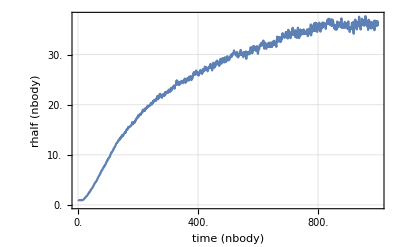

```mathematica
meanRhalfAndTimePlot=ScaledListPlot[meanRhalfAndTime,{$TimeScale,$LengthScale},
FrameLabel->{{"rhalf (nbody)","rhalf (pc)"},{"time (nbody)","time (My)"}},
"ShowAllScales"->True]
```

### Mean rdens

```mathematica
meanRdens=Mean/@DeleteCases[Transpose[data[[All,All,3]]],$Failed,{2}];
```

```mathematica
meanRdensAndTime=Transpose[{timeArray,meanRdens}];
```

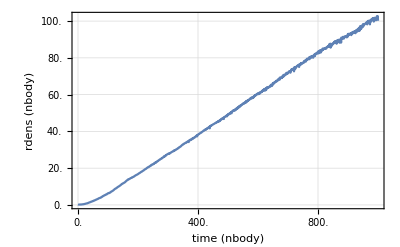

```mathematica
meanRdensAndTimePlot=ScaledListPlot[meanRdensAndTime,{$TimeScale,$LengthScale},
FrameLabel->{{"rdens (nbody)","rdens (pc)"},{"time (nbody)","time (My)"}},"ShowAllScales"->True]
```

## Loading Data

#### Load from OUT3 or MX

```mathematica
(* 8 values: id, pos, vel, mass *)
(* 8 bytes each one *)
```

```mathematica
(numberOfStars*maxNbodyTime*runmax*8*8)/(1024*1024*1024. nbodyStep)
```

2.43187

```mathematica
snapshots=All;
```

```mathematica
(*snapshots=Range[1,maxNbodyTime,10];*)
```

```mathematica
Write[logstream, "computing particles.mx ...."]
```

```mathematica
(* Check also: "particles.bin" *)
If[!FileExistsQ["particles.mx"]
	,
	Print[TimeAndMem[]];
	(*While[Kernels[] == {}, 
		kernels = LaunchKernels[];
		];*)
	kernels = LaunchKernels[];
	Write[logstream, kernels];
	Print["Kernels: ", kernels];
	SetSharedVariable[dirs];
	ParallelEvaluate[AppendTo[$Path, Environment["MYGITDIR"]]];
	ParallelEvaluate[SetDirectory[resultsPath]];
	ParallelNeeds["AstroTools`nbody6`"];
	ParallelNeeds["AstroTools`Utilities`"];
	(particles = 
		Transpose@
		ParallelTable[
			SetDirectory[dirs[[i]]];
			Print["DIR: ", dirs[[i]]];
			{bodys,xs,vs,name} = Flatten[ReadOUT3["OUT3","Snapshots" -> snapshots], 1];
			xs=Partition[#,3]&/@xs;
			vs=Partition[#,3]&/@vs;
			ResetDirectory[]; 
			{bodys,xs,vs,name}
			,
			{i,1,Length[dirs]}]);
	
	Print["Closing kernels ..."];
	CloseKernels[];

	(*-- SAVE to a MX file --*)
	Print["Saving data to MX ... "];
	Print[TimeAndMem[]];
	DumpSave["particles.mx", particles];
	Print[TimeAndMem[]];

	(*-- SAVE to a BIN file --*)
	(* BinarySerializeSave[particles,"particles.bin"]; // AbsoluteTiming *)
	
	,
	
	(*-- Get file from MX --*)
	Print["Loading MX ..."];
	Get["particles.mx"];
] // AbsoluteTiming
```

15:39:31 mem:224.216MB

Kernels: {KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

DIR: ./run-102/

DIR: ./run-117/

DIR: ./run-137/

DIR: ./run-170/

DIR: ./run-195/

DIR: ./run-226/

DIR: ./run-237/

DIR: ./run-249/

DIR: ./run-267/

DIR: ./run-280/

DIR: ./run-295/

DIR: ./run-309/

DIR: ./run-333/

DIR: ./run-364/

DIR: ./run-373/

DIR: ./run-397/

DIR: ./run-416/

DIR: ./run-435/

DIR: ./run-458/

DIR: ./run-469/

DIR: ./run-479/

DIR: ./run-486/

DIR: ./run-494/

DIR: ./run-505/

DIR: ./run-523/

DIR: ./run-530/

DIR: ./run-534/

DIR: ./run-543/

DIR: ./run-555/

DIR: ./run-581/

DIR: ./run-510/

DIR: ./run-379/

DIR: ./run-461/

DIR: ./run-365/

DIR: ./run-126/

DIR: ./run-403/

DIR: ./run-19/

DIR: ./run-524/

DIR: ./run-272/

DIR: ./run-594/

DIR: ./run-104/

DIR: ./run-324/

DIR: ./run-284/

DIR: ./run-251/

DIR: ./run-442/

DIR: ./run-496/

DIR: ./run-487/

DIR: ./run-474/

DIR: ./run-536/

DIR: ./run-138/

DIR: ./run-556/

DIR: ./run-23/

DIR: ./run-417/

DIR: ./run-480/

DIR: ./run-297/

DIR: ./run-228/

DIR: ./run-335/

DIR: ./run-171/

DIR: ./run-531/

DIR: ./run-547/

DIR: ./run-367/

DIR: ./run-463/

DIR: ./run-603/

DIR: ./run-144/

DIR: ./run-389/

DIR: ./run-351/

DIR: ./run-481/

DIR: ./run-511/

DIR: ./run-1/

DIR: ./run-278/

DIR: ./run-286/

DIR: ./run-477/

DIR: ./run-407/

DIR: ./run-229/

DIR: ./run-258/

DIR: ./run-427/

DIR: ./run-52/

DIR: ./run-44/

DIR: ./run-12/

DIR: ./run-10/

DIR: ./run-489/

DIR: ./run-328/

DIR: ./run-542/

DIR: ./run-245/

DIR: ./run-500/

DIR: ./run-553/

DIR: ./run-2/

DIR: ./run-176/

DIR: ./run-563/

DIR: ./run-533/

DIR: ./run-391/

DIR: ./run-485/

DIR: ./run-371/

DIR: ./run-110/

DIR: ./run-165/

DIR: ./run-234/

DIR: ./run-289/

DIR: ./run-35/

DIR: ./run-411/

DIR: ./run-428/

DIR: ./run-455/

DIR: ./run-464/

DIR: ./run-503/

DIR: ./run-522/

DIR: ./run-491/

DIR: ./run-306/

DIR: ./run-27/

DIR: ./run-604/

DIR: ./run-260/

DIR: ./run-478/

DIR: ./run-203/

DIR: ./run-131/

DIR: ./run-185/

DIR: ./run-246/

DIR: ./run-329/

DIR: ./run-623/

DIR: ./run-635/

DIR: ./run-657/

DIR: ./run-685/

DIR: ./run-611/

DIR: ./run-6/

DIR: ./run-707/

DIR: ./run-718/

DIR: ./run-724/

DIR: ./run-736/

DIR: ./run-748/

DIR: ./run-755/

DIR: ./run-771/

DIR: ./run-795/

DIR: ./run-79/

DIR: ./run-810/

DIR: ./run-825/

DIR: ./run-841/

DIR: ./run-854/

DIR: ./run-868/

DIR: ./run-888/

DIR: ./run-902/

DIR: ./run-916/

DIR: ./run-930/

DIR: ./run-941/

DIR: ./run-946/

DIR: ./run-639/

DIR: ./run-665/

DIR: ./run-61/

DIR: ./run-962/

DIR: ./run-965/

DIR: ./run-982/

DIR: ./run-989/

DIR: ./run-711/

DIR: ./run-719/

DIR: ./run-727/

DIR: ./run-744/

DIR: ./run-750/

DIR: ./run-781/

DIR: ./run-806/

DIR: ./run-818/

DIR: ./run-765/

DIR: ./run-625/

DIR: ./run-686/

DIR: ./run-836/

DIR: ./run-702/

DIR: ./run-796/

DIR: ./run-850/

DIR: ./run-864/

DIR: ./run-884/

DIR: ./run-90/

DIR: ./run-93/

DIR: ./run-88/

DIR: ./run-927/

DIR: ./run-81/

DIR: ./run-628/

DIR: ./run-699/

DIR: ./run-974/

DIR: ./run-678/

DIR: ./run-942/

DIR: ./run-751/

DIR: ./run-963/

DIR: ./run-770/

DIR: ./run-80/

DIR: ./run-783/

DIR: ./run-706/

DIR: ./run-840/

DIR: ./run-853/

DIR: ./run-983/

DIR: ./run-996/

DIR: ./run-947/

DIR: ./run-717/

DIR: ./run-722/

DIR: ./run-72/

DIR: ./run-747/

DIR: ./run-797/

DIR: ./run-653/

DIR: ./run-867/

DIR: ./run-914/

DIR: ./run-885/

DIR: ./run-890/

DIR: ./run-940/

DIR: ./run-92/

DIR: ./run-964/

DIR: ./run-97/

DIR: ./run-987/

DIR: ./run-998/

DIR: ./run-945/

DIR: ./run-948/

Closing kernels ...

Saving data to MX ...

15:43:04 mem:10.6469GB

15:58:27 mem:7.92186GB

{1135.26,Null}

```mathematica
Write[logstream, "particles.mx done!"]
```

```mathematica
(* --- serial computation ---
(particles=
Transpose@
Table[SetDirectory[dirs[[i]]];
Print["DIR: ", dirs[[i]]];
{bodys,xs,vs,name}=Flatten[ReadOUT3["OUT3","Snapshots"->All],1];
xs=Partition[#,3]&/@xs;
vs=Partition[#,3]&/@vs;
ResetDirectory[]; 
{bodys,xs,vs,name}
,{i,1,Length[dirs]}]);//AbsoluteTiming *)
```

#### Mem information

```mathematica
TimeAndMem[]
```

15:58:27 mem:7.92186GB

```mathematica
(*PrintArrayInfo[particles]*)
```

```mathematica
DeleteOuts[500]
```

session mem: 7.92186GB

No Out[] greater than 500MB

```mathematica
$numberOfRunsStatus=Dimensions[particles][[2]]
```

204

## Filtering Invalid Data

### Indexes To Extract Data

```mathematica
nbIndexes=Table[Range[maxNbodyTime/nbodyStep+1],{runmax}];
```

```mathematica
nbIndexes//Dimensions
```

{204,1001}

```mathematica
nbIndexes[[1]]//Short
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001}

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001}

### Incomplete runs

```mathematica
particles//Dimensions
```

{4,204,1001}

```mathematica
Length/@particles[[4]]//Union
```

{1001}

```mathematica
(* delete runs that have not complete data *)
maxtimes=Length/@particles[[4]]
```

{1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001}

```mathematica
delPos1=Position[maxtimes,x_/;x<Max[maxtimes]]
```

{}

```mathematica
delPos1//Length
```

0

#### FIX: Delete complete runs

```mathematica
Extract[dirs,delPos1]
```

{}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos1],All,2]
```

{}

```mathematica
dirsToDelete//Length
```

0

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete
```

{}

Opt – Update variables to continue computing

```mathematica
particles//Dimensions
```

{4,204,1001}

```mathematica
dirs=Delete[dirs,delPos1];
runmax=Length[dirs];
particles=Delete[#, delPos1]&/@particles;
nbIndexes=Delete[nbIndexes, delPos1];
nbLenIndexes=Length/@nbIndexes;
parameters=Delete[parameters, delPos1];
```

```mathematica
particles//Dimensions
```

{4,204,1001}

```mathematica
nbIndexes//Length
```

204

```mathematica
parameters//Dimensions
```

{204,6}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 11.0615GB

### Particles in the same position

#### TEST

```mathematica
particles[[All,All,All,1;;numberOfStars]]//Dimensions
```

{4,204,1001,200}

```mathematica
Clear[ceros];
If[!FileExistsQ["ceros.mx"],
ceros=Reap[
Do[
Print["run: ", run];
Do[
With[
{pe=TotalPotentialEnergy[particles[[1,run,t,All]],particles[[2,run,t,All]]]},
If[pe==0.,Sow[{run,t}];Print["CERO AT: ", run];Break[]]
]
,{t,1,nbLenIndexes[[run]]}
],
{run,1,runmax}]
];
DumpSave["ceros.mx", ceros]
,
(*-- Get file from MX --*)
	Print["Loading MX ..."];
	Get["ceros.mx"];
];//AbsoluteTiming
```

run: 1

run: 2

run: 3

run: 4

run: 5

run: 6

run: 7

run: 8

run: 9

run: 10

run: 11

run: 12

run: 13

run: 14

run: 15

run: 16

run: 17

run: 18

run: 19

run: 20

run: 21

run: 22

run: 23

run: 24

run: 25

run: 26

run: 27

run: 28

run: 29

run: 30

run: 31

run: 32

run: 33

run: 34

run: 35

run: 36

run: 37

run: 38

run: 39

run: 40

run: 41

run: 42

run: 43

run: 44

run: 45

run: 46

run: 47

run: 48

run: 49

run: 50

run: 51

run: 52

run: 53

run: 54

run: 55

run: 56

run: 57

run: 58

run: 59

run: 60

run: 61

run: 62

run: 63

run: 64

run: 65

run: 66

run: 67

run: 68

run: 69

run: 70

run: 71

run: 72

run: 73

run: 74

run: 75

run: 76

run: 77

run: 78

run: 79

run: 80

run: 81

run: 82

run: 83

run: 84

run: 85

run: 86

run: 87

run: 88

run: 89

run: 90

run: 91

run: 92

run: 93

run: 94

run: 95

run: 96

run: 97

run: 98

run: 99

run: 100

run: 101

run: 102

run: 103

run: 104

run: 105

run: 106

run: 107

run: 108

run: 109

run: 110

run: 111

run: 112

run: 113

run: 114

run: 115

run: 116

run: 117

run: 118

run: 119

run: 120

run: 121

run: 122

run: 123

run: 124

run: 125

run: 126

run: 127

run: 128

run: 129

run: 130

run: 131

run: 132

run: 133

run: 134

run: 135

run: 136

run: 137

run: 138

run: 139

run: 140

run: 141

run: 142

run: 143

run: 144

run: 145

run: 146

run: 147

run: 148

run: 149

run: 150

run: 151

run: 152

run: 153

run: 154

run: 155

run: 156

run: 157

run: 158

run: 159

run: 160

run: 161

run: 162

run: 163

run: 164

run: 165

run: 166

run: 167

run: 168

run: 169

run: 170

run: 171

run: 172

run: 173

run: 174

run: 175

run: 176

run: 177

run: 178

run: 179

run: 180

run: 181

run: 182

run: 183

run: 184

run: 185

run: 186

run: 187

run: 188

run: 189

run: 190

run: 191

run: 192

run: 193

run: 194

run: 195

run: 196

run: 197

run: 198

run: 199

run: 200

run: 201

run: 202

run: 203

run: 204

{591.96,Null}

```mathematica
ceros[[2]]
```

{}

#### Double check

```mathematica
(*invalid=With[{run=7},Reap[Do[
With[
{pe=TotalPotentialEnergy[particles[[1,run,t,All]],particles[[2,run,t,All]]]},
If[pe==0.,Sow[{run,t}]]
]
,{t,1,nbLenIndexes[[run]]}
]]
];*)
```

```mathematica
(*invalid//Short*)
```

```mathematica
(*With[{run=7, time=1100},
Select[GatherBy[Transpose[{particles[[4,run,time,All]],particles[[2,run,time,All]]}],Last],Length[#]>1&]]*)
```

```mathematica
(*With[
{part1=2,
part2=1,
run=46,
interTime=220
},
vel=Table[{#[part1],#[part2]}&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,run,time,All]],particles[[3,run,time,All]]}]|>),{time,1,nbLenIndexes[[run]],1}];
pos=Table[{#[part1],#[part2]}&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,run,time,All]],particles[[2,run,time,All]]}]|>),{time,1,nbLenIndexes[[run]],1}];

{ListLinePlot[{Norm/@vel[[All,1]],Norm/@vel[[All,2]]},
PlotRange->{{0,1000},{0,100}}],
ListLinePlot[{Norm/@pos[[All,1]],Norm/@pos[[All,2]]},
PlotRange->{{0,1000},{0,50000}},Epilog->InfiniteLine[{{interTime,0},{interTime,1}}]]}
]*)
```

```mathematica
(* testing indexes outside particles range *)
```

```mathematica
(*testing1001=Table[#[1001]&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,2,time,All]],particles[[2,2,time,All]]}]|>),{time,1,nbLenIndexes[[2]],1}];*)
```

```mathematica
(*Position[testimg1001,_Missing]*)
```

```mathematica
(*testing1002=Table[#[1002]&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,2,time,All]],particles[[2,2,time,All]]}]|>),{time,1,nbLenIndexes[[2]],1}];*)
```

```mathematica
(*testing1002[[8]]*)
```

#### FIX 1: Delete complete runs

```mathematica
delPos2=If[ceros[[2]]=={},{},Partition[Union[ceros[[2,1]][[All,1]]],1]];
```

```mathematica
delPos2//Short
```

{}

```mathematica
Extract[dirs,delPos2]
```

{}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos2],All,2]
```

{}

```mathematica
dirsToDelete//Length
```

0

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete;
```

Opt 1 – Delete files to begin from scratch

(* 
	Si dirsToDelete≠0 borrar *.m *.mx 
	generar goodRuns.log y correr nb de nuevo.
*)

FileNames["*.*"]

DeleteFile[#] & /@ FileNames["*.*"]

Opt 2 – Update variables to continue computing

```mathematica
dirs=Delete[dirs,delPos2];
```

```mathematica
runmax=Length[dirs]
```

204

```mathematica
particles//Dimensions
```

{4,204,1001}

```mathematica
particles=Delete[#, delPos2]&/@particles;
```

```mathematica
particles//Dimensions
```

{4,204,1001}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 11.0615GB

```mathematica
nbIndexes=Delete[nbIndexes, delPos2];
```

```mathematica
nbIndexes//Length
```

204

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001}

```mathematica
parameters//Dimensions
```

{204,6}

```mathematica
parameters=Delete[parameters, delPos2];
```

```mathematica
parameters//Dimensions
```

{204,6}

#### FIX 2: Delete specific snapshots (ruled out)

```mathematica
(* We will delete data only for snapshots containg equal positions *)
```

delPos3 = ceros[[2, 1]]

particles = Delete[#, delPos3] & /@ particles;

timeIndexes[[1, 450]]

Complement[Range[1000], timeIndexes[[1]]]

timeIndexes = Delete[timeIndexes, delPos3];

Complement[Range[1000], timeIndexes[[1]]]

nbLenIndexes = Length /@ timeIndexes

### Particles with index 0 / position 0.

#### TEST

```mathematica
(* Delete time snaphots of incorrect data with ceros in the position vector. *)
(* Very strange issue from nbody *)
```

```mathematica
delPos4=Position[particles[[4]],0][[All,{1,2}]];
```

```mathematica
delPos4//Short
```

{{1,1001},{7,24},{10,237},{10,474},{10,475},{10,476},{11,32},{11,482},{11,706},{12,667},{18,842},{18,843},{19,54},{19,113},{24,124},{30,27},{47,68},{47,264},{47,265},{47,266},{49,285},{49,286},{49,289},{49,290},{49,291},{52,141},{52,168},{59,26},{59,34},{59,35},{61,31},{61,52},{61,71},{61,78},{61,121},{61,122},{68,89},{68,90},{68,91},{69,51},{77,78},{77,83},{90,43},{92,84},{92,85},{92,86},{98,31},{98,52},{98,71},{98,78},{98,121},{98,122},{99,757},{100,59},{101,312},{104,254},{108,687},{108,688},{108,689},{109,32},{109,63},{109,67},{109,68},{112,123},{112,124},{112,125},{112,126},{112,127},{112,128},{112,129},{112,130},{112,131},{112,132},{112,133},{112,134},{112,135},{114,143},{118,53},{118,254},{120,81},{120,246},{120,247},{120,248},{120,249},{120,250},{120,251},{120,252},{120,253},{120,254},{120,255},{120,256},{120,257},{120,258},{120,259},{120,260},{120,261},{120,262},{120,263},{120,264},{120,633},{120,634},{125,79},{126,594},{126,595},{126,596},{126,597},{132,347},{132,348},{132,349},{132,350},{132,351},{132,378},{132,379},{132,380},{132,381},{133,701},{134,22},{134,155},{134,156},{134,157},{134,158},{134,159},{134,160},{139,124},{139,598},{141,129},{141,130},{141,131},{141,132},{141,133},{141,134},{141,135},{141,136},{141,137},{141,138},{141,139},{141,140},{141,141},{141,142},{141,143},{141,144},{141,145},{141,146},{141,147},{141,148},{141,149},{141,150},{141,151},{141,152},{141,153},{141,154},{141,155},{141,156},{141,157},{141,158},{141,159},{141,160},{141,161},{141,162},{141,163},{141,164},{141,165},{141,166},{141,167},{141,168},{141,169},{141,170},{141,171},{141,172},{141,173},{141,174},{141,175},{141,176},{141,177},{141,178},{141,179},{141,180},{141,181},{141,182},{145,362},{145,363},{145,364},{145,365},{145,366},{145,367},{145,368},{145,369},{145,370},{145,371},{145,372},{145,373},{145,374},{145,375},{145,376},{145,377},{145,378},{145,379},{145,380},{145,381},{145,382},{145,383},{145,384},{145,385},{145,386},{145,387},{145,388},{145,389},{145,390},{145,391},{145,392},{145,393},{145,394},{145,395},{145,396},{145,397},{145,398},{145,399},{145,400},{145,401},{145,402},{145,403},{145,404},{145,405},{145,406},{145,407},{145,408},{145,409},{145,410},{145,411},{145,412},{145,413},{145,414},{145,415},{145,416},{145,417},{145,418},{145,419},{145,420},{145,421},{145,422},{145,423},{145,424},{145,425},{145,426},{145,427},{145,428},{145,429},{145,430},{145,431},{145,432},{145,433},{145,434},{145,435},{145,436},{145,437},{145,438},{145,439},{145,440},{145,441},{145,442},{145,443},{145,444},{145,445},{145,446},{145,447},{145,448},{145,449},{145,450},{145,451},{145,452},{145,453},{145,454},{145,455},{145,456},{145,457},{145,458},{145,459},{145,460},{145,461},{145,462},{145,463},{145,464},{145,465},{145,466},{145,467},{145,468},{145,469},{145,470},{145,471},{145,472},{145,473},{145,474},{145,475},{145,476},{145,477},{145,478},{145,479},{145,480},{145,481},{145,482},{145,483},{145,484},{145,485},{145,486},{145,487},{145,488},{145,489},{145,490},{145,491},{145,492},{145,493},{145,494},{145,495},{145,496},{145,497},{145,498},{145,499},{145,500},{145,501},{145,502},{145,503},{145,504},{145,505},{145,506},{145,507},{145,508},{145,509},{145,510},{145,511},{145,512},{145,513},{145,514},{145,515},{145,516},{145,517},{145,518},{145,519},{145,520},{145,521},{145,522},{145,523},{145,524},{145,525},{145,526},{145,527},{145,528},{145,529},{145,530},{145,531},{145,532},{145,533},{145,534},{145,535},{145,536},{145,537},{145,538},{145,539},{145,540},{145,541},{145,542},{145,543},{145,544},{145,545},{145,546},{145,547},{145,548},{145,549},{145,550},{145,551},{145,552},{145,553},{145,554},{145,555},{145,556},{145,557},{145,558},{145,559},{145,560},{145,561},{145,562},{145,563},{145,564},{145,565},{145,566},{145,567},{145,568},{145,569},{145,570},{145,571},{145,572},{145,573},{145,574},{145,575},{145,576},{145,577},{145,578},{145,579},{145,580},{145,581},{145,582},{145,583},{145,584},{145,585},{145,586},{145,587},{145,588},{145,589},{145,590},{145,591},{145,592},{145,593},{145,594},{145,595},{145,596},{145,597},{145,598},{145,599},{145,600},{145,601},{145,602},{145,603},{145,604},{145,605},{145,606},{145,607},{145,608},{145,609},{145,610},{145,611},{145,612},{145,613},{145,614},{145,615},{145,616},{145,617},{145,618},{145,619},{145,620},{145,621},{145,622},{145,623},{145,624},{145,625},{145,626},{145,627},{145,628},{145,629},{145,630},{145,631},{145,632},{145,633},{145,634},{145,635},{145,636},{145,637},{145,638},{145,639},{145,640},{145,641},{145,642},{145,643},{145,644},{145,645},{145,646},{145,647},{145,648},{145,649},{145,650},{145,651},{145,652},{145,653},{145,654},{145,655},{145,656},{145,657},{145,658},{145,659},{145,660},{145,661},{145,662},{145,663},{145,664},{145,665},{145,666},{145,667},{145,668},{145,669},{145,670},{145,671},{145,672},{145,673},{145,674},{145,675},{145,676},{145,677},{145,678},{145,679},{145,680},{145,681},{145,682},{145,683},{145,684},{145,685},{145,686},{145,687},{145,688},{145,689},{145,690},{145,691},{145,692},{145,693},{145,694},{145,695},{145,696},{145,697},{145,698},{145,699},{145,700},{145,701},{145,702},{145,703},{145,704},{145,705},{145,706},{145,707},{145,708},{145,709},{145,710},{145,711},{145,712},{145,713},{145,714},{145,715},{145,716},{145,717},{145,718},{145,719},{145,720},{145,721},{145,722},{145,723},{145,724},{145,725},{145,726},{145,727},{145,728},{145,729},{145,730},{145,731},{145,732},{145,733},{145,734},{145,735},{145,736},{145,737},{145,738},{145,739},{145,740},{145,741},{145,742},{145,743},{145,744},{145,745},{145,746},{145,747},{145,748},{145,749},{145,750},{145,751},{145,752},{145,753},{145,754},{145,755},{145,756},{145,757},{145,758},{145,759},{145,760},{145,761},{145,762},{145,763},{145,764},{145,765},{145,766},{145,767},{145,768},{145,769},{145,770},{145,771},{145,772},{145,773},{145,774},{145,775},{145,776},{145,777},{145,778},{145,779},{145,780},{145,781},{145,782},{145,783},{145,784},{145,785},{145,786},{145,787},{145,788},{145,789},{145,790},{145,791},{145,792},{145,793},{145,794},{145,795},{145,796},{145,797},{145,798},{145,799},{145,800},{145,801},{145,802},{145,803},{145,804},{145,805},{145,806},{145,807},{145,808},{145,809},{145,810},{145,811},{145,812},{145,813},{145,814},{145,815},{145,816},{145,817},{145,818},{145,819},{145,820},{145,821},{145,822},{145,823},{145,824},{145,825},{145,826},{145,827},{145,828},{145,829},{145,830},{145,831},{145,832},{145,833},{145,834},{145,835},{145,836},{145,837},{145,838},{145,839},{145,840},{145,841},{145,842},{145,843},{145,844},{145,845},{145,846},{145,847},{145,848},{145,849},{145,850},{145,851},{145,852},{145,853},{145,854},{145,855},{145,856},{145,857},{145,858},{145,859},{145,860},{145,861},{145,862},{145,863},{145,864},{145,865},{145,866},{145,867},{145,868},{145,869},{145,870},{145,871},{145,872},{145,873},{145,874},{145,875},{145,876},{145,877},{145,878},{145,879},{145,880},{145,881},{145,882},{145,883},{145,884},{145,885},{145,886},{145,887},{145,888},{145,889},{145,890},{145,891},{145,892},{145,893},{145,894},{145,895},{145,896},{145,897},{145,898},{145,899},{145,900},{145,901},{145,902},{145,903},{145,904},{145,905},{145,906},{145,907},{145,908},{145,909},{145,910},{145,911},{145,912},{145,913},{145,914},{145,915},{145,916},{145,917},{145,918},{145,919},{145,920},{145,921},{145,922},{145,923},{145,924},{145,925},{145,926},{145,927},{145,928},{145,929},{145,930},{145,931},{145,932},{145,933},{145,934},{145,935},{145,936},{145,937},{145,938},{145,939},{145,940},{145,941},{145,942},{145,943},{145,944},{145,945},{145,946},{145,947},{145,948},{145,949},{145,950},{145,951},{145,952},{145,953},{145,954},{145,955},{145,956},{145,957},{145,958},{145,959},{145,960},{145,961},{145,962},{145,963},{145,964},{145,965},{145,966},{145,967},{145,968},{145,969},{145,970},{145,971},{145,972},{145,973},{145,974},{145,975},{145,976},{145,977},{145,978},{145,979},{145,980},{145,981},{145,982},{145,983},{145,984},{145,985},{145,986},{145,987},{145,988},{145,989},{145,990},{145,991},{145,992},{145,993},{145,994},{145,995},{145,996},{145,997},{145,998},{145,999},{145,1000},{145,1001},{150,105},{156,179},{156,180},{156,181},{156,182},{156,183},{162,36},{164,45},{167,119},{170,493},{170,494},{170,495},{170,496},{170,497},{170,498},{170,499},{170,502},{175,39},{176,30},{176,112},{176,113},{176,114},{176,115},{176,116},{183,41},{184,55},{184,56},{184,57},{184,65},{184,66},{184,67},{184,69},{184,70},{184,71},{184,72},{184,73},{184,74},{186,871},{189,119},{190,31},{191,72},{191,248},{191,406},{196,249},{197,112},{198,391},{198,392},{202,85},{204,107},{204,108}}

```mathematica
delPos4[[All,1]]//Union
```

{1,7,10,11,12,18,19,24,30,47,49,52,59,61,68,69,77,90,92,98,99,100,101,104,108,109,112,114,118,120,125,126,132,133,134,139,141,145,150,156,162,164,167,170,175,176,183,184,186,189,190,191,196,197,198,202,204}

```mathematica
delPos4[[All,1]]//Union//Length
```

57

```mathematica
(* NICE runs *)
Complement[Range[runmax],delPos4[[All,1]]//Union]
```

{2,3,4,5,6,8,9,13,14,15,16,17,20,21,22,23,25,26,27,28,29,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,48,50,51,53,54,55,56,57,58,60,62,63,64,65,66,67,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,88,89,91,93,94,95,96,97,102,103,105,106,107,110,111,113,115,116,117,119,121,122,123,124,127,128,129,130,131,135,136,137,138,140,142,143,144,146,147,148,149,151,152,153,154,155,157,158,159,160,161,163,165,166,168,169,171,172,173,174,177,178,179,180,181,182,185,187,188,192,193,194,195,199,200,201,203}

```mathematica
(* Consistent with non missing IDs *)
moreIDS=Table[Position[Complement[Range[numberOfStars],#]&/@particles[[4,run,All,All]],x_/;x≠{},{1}],{run,runmax}];
Position[moreIDS,{}]//Flatten
```

{2,3,4,5,6,8,9,13,14,15,16,17,20,21,22,23,25,26,27,28,29,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,48,50,51,53,54,55,56,57,58,60,62,63,64,65,66,67,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,88,89,91,93,94,95,96,97,102,103,105,106,107,110,111,113,115,116,117,119,121,122,123,124,127,128,129,130,131,135,136,137,138,140,142,143,144,146,147,148,149,151,152,153,154,155,157,158,159,160,161,163,165,166,168,169,171,172,173,174,177,178,179,180,181,182,185,187,188,192,193,194,195,199,200,201,203}

```mathematica
bad=delPos4[[All,1]]//Union
good=Position[moreIDS,{}]//Flatten
```

{1,7,10,11,12,18,19,24,30,47,49,52,59,61,68,69,77,90,92,98,99,100,101,104,108,109,112,114,118,120,125,126,132,133,134,139,141,145,150,156,162,164,167,170,175,176,183,184,186,189,190,191,196,197,198,202,204}

{2,3,4,5,6,8,9,13,14,15,16,17,20,21,22,23,25,26,27,28,29,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,48,50,51,53,54,55,56,57,58,60,62,63,64,65,66,67,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,88,89,91,93,94,95,96,97,102,103,105,106,107,110,111,113,115,116,117,119,121,122,123,124,127,128,129,130,131,135,136,137,138,140,142,143,144,146,147,148,149,151,152,153,154,155,157,158,159,160,161,163,165,166,168,169,171,172,173,174,177,178,179,180,181,182,185,187,188,192,193,194,195,199,200,201,203}

```mathematica
(* Runs to be fixed: good + partOfBad = 50 *)
numToFix=Which[
Length[good]≥50,0,
Length[good]<50,50-Length[good]]
```

0

```mathematica
runsToFix=TakeSmallestBy[delPos4[[All,1]]//Tally,Last,UpTo[numToFix]]
```

{}

```mathematica
Complement[good,Take[good,50]]
```

{65,66,67,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,88,89,91,93,94,95,96,97,102,103,105,106,107,110,111,113,115,116,117,119,121,122,123,124,127,128,129,130,131,135,136,137,138,140,142,143,144,146,147,148,149,151,152,153,154,155,157,158,159,160,161,163,165,166,168,169,171,172,173,174,177,178,179,180,181,182,185,187,188,192,193,194,195,199,200,201,203}

```mathematica
(* Runs to be deleted *)
runsToDelete=If[Length[good]≥50,
Union[bad,Complement[good,Take[good,50]]],
SortBy[Complement[delPos4[[All,1]]//Tally,runsToFix],Last][[All,1]]
]
```

{1,7,10,11,12,18,19,24,30,47,49,52,59,61,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204}

#### FIX Part–1: Delete complete runs

```mathematica
delPos5=Partition[runsToDelete,1]
```

{{1},{7},{10},{11},{12},{18},{19},{24},{30},{47},{49},{52},{59},{61},{65},{66},{67},{68},{69},{70},{71},{72},{73},{74},{75},{76},{77},{78},{79},{80},{81},{82},{83},{84},{85},{86},{87},{88},{89},{90},{91},{92},{93},{94},{95},{96},{97},{98},{99},{100},{101},{102},{103},{104},{105},{106},{107},{108},{109},{110},{111},{112},{113},{114},{115},{116},{117},{118},{119},{120},{121},{122},{123},{124},{125},{126},{127},{128},{129},{130},{131},{132},{133},{134},{135},{136},{137},{138},{139},{140},{141},{142},{143},{144},{145},{146},{147},{148},{149},{150},{151},{152},{153},{154},{155},{156},{157},{158},{159},{160},{161},{162},{163},{164},{165},{166},{167},{168},{169},{170},{171},{172},{173},{174},{175},{176},{177},{178},{179},{180},{181},{182},{183},{184},{185},{186},{187},{188},{189},{190},{191},{192},{193},{194},{195},{196},{197},{198},{199},{200},{201},{202},{203},{204}}

```mathematica
delPos5//Short
```

{{1},{7},{10},{11},{12},{18},{19},{24},{30},{47},{49},{52},{59},{61},{65},{66},{67},{68},{69},{70},{71},{72},{73},{74},{75},{76},{77},{78},{79},{80},{81},{82},{83},{84},{85},{86},{87},{88},{89},{90},{91},{92},{93},{94},{95},{96},{97},{98},{99},{100},{101},{102},{103},{104},{105},{106},{107},{108},{109},{110},{111},{112},{113},{114},{115},{116},{117},{118},{119},{120},{121},{122},{123},{124},{125},{126},{127},{128},{129},{130},{131},{132},{133},{134},{135},{136},{137},{138},{139},{140},{141},{142},{143},{144},{145},{146},{147},{148},{149},{150},{151},{152},{153},{154},{155},{156},{157},{158},{159},{160},{161},{162},{163},{164},{165},{166},{167},{168},{169},{170},{171},{172},{173},{174},{175},{176},{177},{178},{179},{180},{181},{182},{183},{184},{185},{186},{187},{188},{189},{190},{191},{192},{193},{194},{195},{196},{197},{198},{199},{200},{201},{202},{203},{204}}

```mathematica
delPos5//Length
```

154

```mathematica
Extract[dirs,delPos5]
```

{./run-102/,./run-12/,./run-138/,./run-144/,./run-165/,./run-19/,./run-1/,./run-234/,./run-251/,./run-328/,./run-333/,./run-35/,./run-389/,./run-397/,./run-416/,./run-417/,./run-427/,./run-428/,./run-435/,./run-442/,./run-44/,./run-455/,./run-458/,./run-461/,./run-463/,./run-464/,./run-469/,./run-474/,./run-477/,./run-478/,./run-479/,./run-480/,./run-481/,./run-485/,./run-486/,./run-487/,./run-489/,./run-491/,./run-494/,./run-496/,./run-500/,./run-503/,./run-505/,./run-510/,./run-511/,./run-522/,./run-523/,./run-524/,./run-52/,./run-530/,./run-531/,./run-533/,./run-534/,./run-536/,./run-542/,./run-543/,./run-547/,./run-553/,./run-555/,./run-556/,./run-563/,./run-581/,./run-594/,./run-603/,./run-604/,./run-611/,./run-61/,./run-623/,./run-625/,./run-628/,./run-635/,./run-639/,./run-653/,./run-657/,./run-665/,./run-678/,./run-685/,./run-686/,./run-699/,./run-6/,./run-702/,./run-706/,./run-707/,./run-711/,./run-717/,./run-718/,./run-719/,./run-722/,./run-724/,./run-727/,./run-72/,./run-736/,./run-744/,./run-747/,./run-748/,./run-750/,./run-751/,./run-755/,./run-765/,./run-770/,./run-771/,./run-781/,./run-783/,./run-795/,./run-796/,./run-797/,./run-79/,./run-806/,./run-80/,./run-810/,./run-818/,./run-81/,./run-825/,./run-836/,./run-840/,./run-841/,./run-850/,./run-853/,./run-854/,./run-864/,./run-867/,./run-868/,./run-884/,./run-885/,./run-888/,./run-88/,./run-890/,./run-902/,./run-90/,./run-914/,./run-916/,./run-927/,./run-92/,./run-930/,./run-93/,./run-940/,./run-941/,./run-942/,./run-945/,./run-946/,./run-947/,./run-948/,./run-962/,./run-963/,./run-964/,./run-965/,./run-974/,./run-97/,./run-982/,./run-983/,./run-987/,./run-989/,./run-996/,./run-998/}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos5],All,2]
```

{run-102,run-12,run-138,run-144,run-165,run-19,run-1,run-234,run-251,run-328,run-333,run-35,run-389,run-397,run-416,run-417,run-427,run-428,run-435,run-442,run-44,run-455,run-458,run-461,run-463,run-464,run-469,run-474,run-477,run-478,run-479,run-480,run-481,run-485,run-486,run-487,run-489,run-491,run-494,run-496,run-500,run-503,run-505,run-510,run-511,run-522,run-523,run-524,run-52,run-530,run-531,run-533,run-534,run-536,run-542,run-543,run-547,run-553,run-555,run-556,run-563,run-581,run-594,run-603,run-604,run-611,run-61,run-623,run-625,run-628,run-635,run-639,run-653,run-657,run-665,run-678,run-685,run-686,run-699,run-6,run-702,run-706,run-707,run-711,run-717,run-718,run-719,run-722,run-724,run-727,run-72,run-736,run-744,run-747,run-748,run-750,run-751,run-755,run-765,run-770,run-771,run-781,run-783,run-795,run-796,run-797,run-79,run-806,run-80,run-810,run-818,run-81,run-825,run-836,run-840,run-841,run-850,run-853,run-854,run-864,run-867,run-868,run-884,run-885,run-888,run-88,run-890,run-902,run-90,run-914,run-916,run-927,run-92,run-930,run-93,run-940,run-941,run-942,run-945,run-946,run-947,run-948,run-962,run-963,run-964,run-965,run-974,run-97,run-982,run-983,run-987,run-989,run-996,run-998}

```mathematica
dirsToDelete//Length
```

154

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete;
```

Opt 1 – Delete files to begin from scratch

FileNames["*.*"]

DeleteFile[#] & /@ FileNames["*.*"]

Opt 2 – Update variables to continue computing

```mathematica
dirs=Delete[dirs,delPos5]
```

{./run-104/,./run-10/,./run-110/,./run-117/,./run-126/,./run-131/,./run-137/,./run-170/,./run-171/,./run-176/,./run-185/,./run-195/,./run-203/,./run-226/,./run-228/,./run-229/,./run-237/,./run-23/,./run-245/,./run-246/,./run-249/,./run-258/,./run-260/,./run-267/,./run-272/,./run-278/,./run-27/,./run-280/,./run-284/,./run-286/,./run-289/,./run-295/,./run-297/,./run-2/,./run-306/,./run-309/,./run-324/,./run-329/,./run-335/,./run-351/,./run-364/,./run-365/,./run-367/,./run-371/,./run-373/,./run-379/,./run-391/,./run-403/,./run-407/,./run-411/}

```mathematica
runmax=Length[dirs]
```

50

```mathematica
particles//Dimensions
```

{4,204,1001}

```mathematica
particles=Delete[#, delPos5]&/@particles;
```

```mathematica
particles//Dimensions
```

{4,50,1001}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 2.71233GB

```mathematica
nbIndexes=Delete[nbIndexes, delPos5];
```

```mathematica
nbIndexes//Length
```

50

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001}

```mathematica
parameters//Dimensions
```

{204,6}

```mathematica
parameters=Delete[parameters, delPos5];
```

```mathematica
parameters//Dimensions
```

{50,6}

#### FIX Part–2: Delete specific snaphots

```mathematica
delPos6=Position[particles[[4]],0][[All,{1,2}]]
```

{}

```mathematica
delPos6[[All,1]]//Union
```

{}

```mathematica
%//Length
```

0

```mathematica
particles=Delete[#, delPos6]&/@particles;
```

```mathematica
nbIndexes=Delete[nbIndexes, delPos6];
```

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001}

```mathematica
nbLenIndexes//Length
```

50

### Position high values (test only)

With lack those cases happens together with the issues in the previous section. Fixing there makes fixed here.

highPos=Position[Map[Norm,particles[[2,All,1;;50,All]],{3}],x_/;x>10.^6]

particles[[2, 5, 4, 2]] // Norm

highPos[[All, 1]] // Union

## index ↔ nbIndex ↔ nbTime

```mathematica
Length/@nbIndexes
```

{1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001,1001}

```mathematica
(* Indexes that are missing at least in one run *)
delPos6[[All,2]]//Union//Short
```

{}

```mathematica
%//Length
```

0

```mathematica
(* Indexes with complete data across runs *)
nbCompleteIndexes=Complement[Range[maxNbodyTime/nbodyStep+1],delPos6[[All,2]]//Union];
nbCompleteIndexes//Short
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001}

```mathematica
(* Number of times with common data *)
nbCompleteIndexes//Length
```

1001

```mathematica
(* Select a set of valid indexes with more or less equal spacing using nearest *)
```

```mathematica
(numberOfStars*numberOfStars*maxNbodyTime*runmax*1)/(1024*1024*1024. nbodyStep*10)
```

0.186265

```mathematica
maxNbodyTime/nbodyStep
```

1000

```mathematica
nbIndexesSubset=Flatten[Table[Nearest[nbCompleteIndexes,i,1],{i,0,maxNbodyTime/nbodyStep+1,5}]]
```

{1,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,255,260,265,270,275,280,285,290,295,300,305,310,315,320,325,330,335,340,345,350,355,360,365,370,375,380,385,390,395,400,405,410,415,420,425,430,435,440,445,450,455,460,465,470,475,480,485,490,495,500,505,510,515,520,525,530,535,540,545,550,555,560,565,570,575,580,585,590,595,600,605,610,615,620,625,630,635,640,645,650,655,660,665,670,675,680,685,690,695,700,705,710,715,720,725,730,735,740,745,750,755,760,765,770,775,780,785,790,795,800,805,810,815,820,825,830,835,840,845,850,855,860,865,870,875,880,885,890,895,900,905,910,915,920,925,930,935,940,945,950,955,960,965,970,975,980,985,990,995,1000}

```mathematica
%//Length
```

201

```mathematica
NBIndexToNBTime[indx_]:=nbodyStep(indx-1)
```

```mathematica
nbTimeSubset=NBIndexToNBTime[nbIndexesSubset]
```

{0,4,9,14,19,24,29,34,39,44,49,54,59,64,69,74,79,84,89,94,99,104,109,114,119,124,129,134,139,144,149,154,159,164,169,174,179,184,189,194,199,204,209,214,219,224,229,234,239,244,249,254,259,264,269,274,279,284,289,294,299,304,309,314,319,324,329,334,339,344,349,354,359,364,369,374,379,384,389,394,399,404,409,414,419,424,429,434,439,444,449,454,459,464,469,474,479,484,489,494,499,504,509,514,519,524,529,534,539,544,549,554,559,564,569,574,579,584,589,594,599,604,609,614,619,624,629,634,639,644,649,654,659,664,669,674,679,684,689,694,699,704,709,714,719,724,729,734,739,744,749,754,759,764,769,774,779,784,789,794,799,804,809,814,819,824,829,834,839,844,849,854,859,864,869,874,879,884,889,894,899,904,909,914,919,924,929,934,939,944,949,954,959,964,969,974,979,984,989,994,999}

```mathematica
IndexToNBIndex=MapThread[AssociationThread, {Range /@ nbLenIndexes, nbIndexes}];
```

```mathematica
100/.IndexToNBIndex
```

{100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100}

```mathematica
NBIndexToIndex=MapThread[Merge[{#1,#2},First]&,{MapThread[AssociationThread, {nbIndexes,Range /@ nbLenIndexes}],MapThread[AssociationThread, {Complement[Range[maxNbodyTime/nbodyStep+1],#]&/@nbIndexes,Table[Missing[], {maxNbodyTime/nbodyStep+1-#}]&/@nbLenIndexes}]}];
```

```mathematica
Position[NBIndexToIndex,_Missing]
```

{}

```mathematica
102/.NBIndexToIndex
```

{102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102}

```mathematica
clusterSlides[run_]:=nbIndexesSubset/.NBIndexToIndex[[run]]
```

```mathematica
nbIndexArray=Range[1,maxNbodyTime/nbodyStep+1];
```

## Close

```mathematica
Print["len in goodRubs:: ",Length[StringSplit[Import["goodRuns.log","String"],"\n"]]];
Print["len in particles:: ",$numberOfRunsStatus]
If[$numberOfRunsStatus>50,
Import["!../run2end.sh","String"];
Print["deleted: ",FileNames[{"*.m","*.mx"}]];
DeleteFile[#]&/@FileNames[{"*.m","*.mx"}]
]
```

len in goodRubs:: 204

len in particles:: 204

deleted: {ceros.mx,nbody6-data.mx,particles.mx}

{Null,Null,Null}

```mathematica
Write[logstream, "End log ...."]
```

```mathematica
Close[logstream]
```

/home/cesarg/git/workspace/nbody6/isolated/scripts/FilterAndTest/nbstatus200.log